Извлекая всю пользу из данных задачи, можно достичь уравнения, выражающее расстояние x по горизонтали от основания до места i-го бабаха. К сожалению, оно решается только численно.

```mathematica
v0=Table[6+4i,{i,1,19}]
```

{10,14,18,22,26,30,34,38,42,46,50,54,58,62,66,70,74,78,82}

```mathematica
(1.5-(g l(π/2-1.5)^2)/(2 v0^2 Cos[1.5]))/Degree/.g->9.8
```

{85.8023,85.7793,85.7687,85.7606,85.753,85.7451,85.7368,85.7282,85.7195,85.711,85.7031,85.6962,85.6904,85.6857,85.682,85.6788,85.6755,85.6709,85.6625}

```mathematica
Table[ϕ[[i,2]],{i,1,19}]
```

{85.7915,85.7645,85.7517,85.7419,85.7326,85.7229,85.7126,85.7018,85.6907,85.6797,85.6695,85.6604,85.6528,85.6466,85.6416,85.6373,85.6328,85.6266,85.6151}

```mathematica
Table[ψ[[i,4]],{i,1,19}]
```

{85.7918,85.7648,85.7521,85.7423,85.733,85.7234,85.7131,85.7023,85.6912,85.6803,85.6701,85.661,85.6534,85.6472,85.6423,85.638,85.6335,85.6273,85.6159}

```mathematica
x=Table[z/.NSolve[z^2(1+(Tan[α]-(g z)/(2 v0[[i]]^2 Cos[α]^2))^2)==l[[i]]^2/.α->1.5/.g->9.8,z],{i,1,19}]
```

{{-0.04863,0.0521426,1.43824-0.0889645 ⅈ,1.43824+0.0889645 ⅈ},{-0.110266,0.119595,2.81774-0.164268 ⅈ,2.81774+0.164268 ⅈ},{-0.193644,0.211148,4.65685-0.26252 ⅈ,4.65685+0.26252 ⅈ},{-0.302087,0.33073,6.95528-0.381019 ⅈ,6.95528+0.381019 ⅈ},{-0.438768,0.482213,9.71268-0.51635 ⅈ,9.71268+0.51635 ⅈ},{-0.607181,0.669942,12.9286-0.664089 ⅈ,12.9286+0.664089 ⅈ},{-0.810916,0.89847,16.6026-0.818776 ⅈ,16.6026+0.818776 ⅈ},{-1.0532,1.172,20.7342-0.974163 ⅈ,20.7342+0.974163 ⅈ},{-1.33624,1.49355,25.3229-1.12391 ⅈ,25.3229+1.12391 ⅈ},{-1.66063,1.86415,30.3686-1.26271 ⅈ,30.3686+1.26271 ⅈ},{-2.02506,2.28237,35.8713-1.38777 ⅈ,35.8713+1.38777 ⅈ},{-2.42655,2.74456,41.8314-1.49984 ⅈ,41.8314+1.49984 ⅈ},{-2.86143,3.24602,48.2493-1.60312 ⅈ,48.2493+1.60312 ⅈ},{-3.32663,3.78274,55.1255-1.70322 ⅈ,55.1255+1.70322 ⅈ},{-3.82118,4.35339,62.4603-1.80283 ⅈ,62.4603+1.80283 ⅈ},{-4.34801,4.96173,70.2531-1.89458 ⅈ,70.2531+1.89458 ⅈ},{-4.91675,5.62033,78.5026-1.94779 ⅈ,78.5026+1.94779 ⅈ},{-5.55077,6.36006,87.205-1.86871 ⅈ,87.205+1.86871 ⅈ},{-6.31311,7.26501,96.3497-1.23444 ⅈ,96.3497+1.23444 ⅈ}}

```mathematica
Table[x[[i,1]] Tan[α]-(g x[[i,1]]^2)/(2 v0[[i]]^2 Cos[α]^2)/.g->9.8/.α->1.5,{i,1,19}]
```

{-0.70891,-1.61566,-2.84399,-4.44449,-6.46614,-8.96326,-11.9921,-15.6038,-19.834,-24.6935,-30.1626,-36.1953,-42.7337,-49.7294,-57.1665,-65.0912,-73.6562,-83.233,-94.8283}

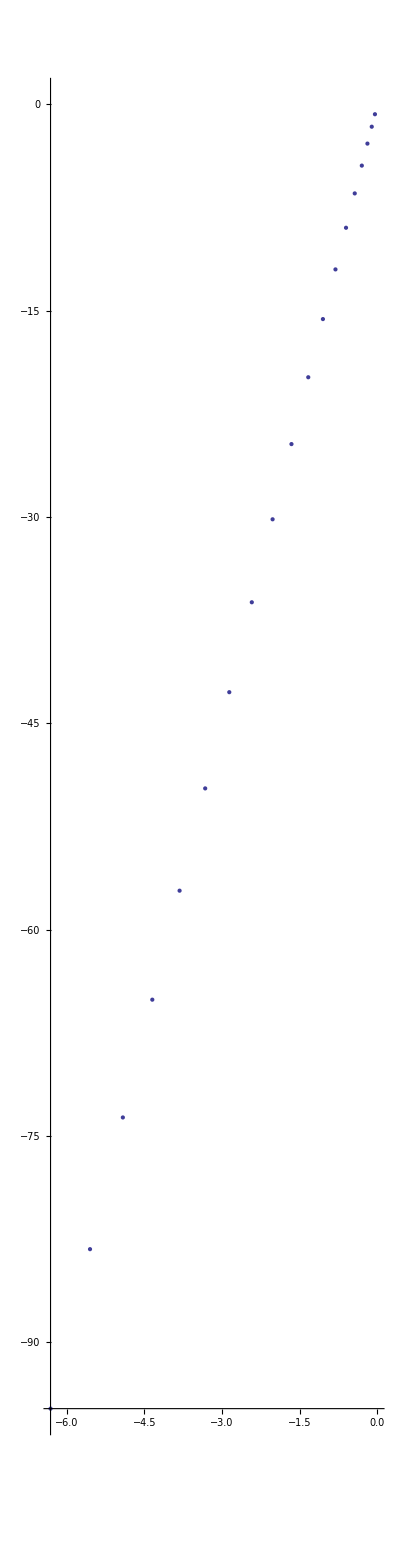

```mathematica
ListPlot[Table[{x[[i,1]],%13[[i]]},{i,1,19}],AspectRatio->10]
```

Part::pspec: Part specification i is neither a machine-sized integer nor a list of machine-sized integers.

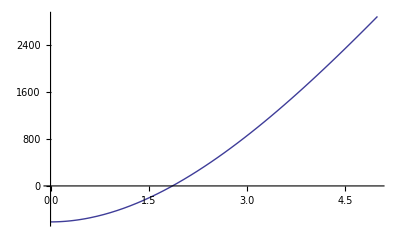

```mathematica
Plot[z^2(1+(Tan[α]-(g z)/(2 v0[[i]]^2 Cos[α]^2))^2)-l[[i]]^2/.α->1.5/.g->9.8/.i->10,{z,0,5}]
```

```mathematica
x={0.052142626296960114,0.11959498209089094,0.21114820760623643,0.33072952562902247,0.48221330153146114,0.6699422615547194,0.8984701400616915,1.171997719314386,1.4935485647826672,1.8641545315817787,2.2823733227384553,2.744557817528493,3.2460165174720528,3.782740832679835,4.353394645862412,4.9617267179498175,5.620334799907464,6.3600601205992735,7.2650056210368215}
```

{0.0521426,0.119595,0.211148,0.33073,0.482213,0.669942,0.89847,1.172,1.49355,1.86415,2.28237,2.74456,3.24602,3.78274,4.35339,4.96173,5.62033,6.36006,7.26501}

Далее используем теорему Пифагора и находим соответствующие вертикальные расстояния:

```mathematica
h=√(l^2-x^2)
```

{{0.70891,0.70866,0.102242+1.25147 ⅈ,0.102242-1.25147 ⅈ},{1.61566,1.615,0.200482+2.30875 ⅈ,0.200482-2.30875 ⅈ},{2.84399,2.84274,0.331483+3.68801 ⅈ,0.331483-3.68801 ⅈ},{4.44449,4.44245,0.495268+5.35082 ⅈ,0.495268-5.35082 ⅈ},{6.46614,6.46305,0.691861+7.24877 ⅈ,0.691861-7.24877 ⅈ},{8.96326,8.95879,0.921293+9.31924 ⅈ,0.921293-9.31924 ⅈ},{11.9921,11.9859,1.1836+11.4852 ⅈ,1.1836-11.4852 ⅈ},{15.6038,15.5953,1.47881+13.6586 ⅈ,1.47881-13.6586 ⅈ},{19.834,19.8228,1.80696+15.7505 ⅈ,1.80696-15.7505 ⅈ},{24.6935,24.679,2.16807+17.6871 ⅈ,2.16807-17.6871 ⅈ},{30.1626,30.1442,2.56212+19.4296 ⅈ,2.56212-19.4296 ⅈ},{36.1953,36.1725,2.9891+20.9897 ⅈ,2.9891-20.9897 ⅈ},{42.7337,42.7062,3.44897+22.4269 ⅈ,3.44897-22.4269 ⅈ},{49.7294,49.6967,3.9417+23.8199 ⅈ,3.9417-23.8199 ⅈ},{57.1665,57.1285,4.46727+25.2068 ⅈ,4.46727-25.2068 ⅈ},{65.0912,65.0473,5.0257+26.4839 ⅈ,5.0257-26.4839 ⅈ},{73.6562,73.6058,5.61712+27.2215 ⅈ,5.61712-27.2215 ⅈ},{83.233,83.1751,6.24178+26.108 ⅈ,6.24178-26.108 ⅈ},{94.8283,94.7601,6.90046+17.2363 ⅈ,6.90046-17.2363 ⅈ}}

```mathematica
h={0.708660284126926,1.6149978875090456,2.842739129664323,4.442445998374905,6.463045795283067,8.958785621175615,11.985872169242318,15.595323845176216,19.822813969884187,24.67899467912709,30.144218388700207,36.17252900525816,42.70621595421793,49.69674347522961,57.12846794608951,65.04733742180677,73.60583537157193,83.17509047588925,94.76011372178858}
```

{0.70866,1.615,2.84274,4.44245,6.46305,8.95879,11.9859,15.5953,19.8228,24.679,30.1442,36.1725,42.7062,49.6967,57.1285,65.0473,73.6058,83.1751,94.7601}

```mathematica
l=√(h^2+x^2)
```

```mathematica
l={0.710576,1.61942,2.85057,4.45474,6.48101,8.9838,12.0195,15.6393,19.879,24.7493,30.2305,36.2765,42.8294,49.8405,57.2941,65.2363,73.8201,83.4179,95.0382}
```

{0.710576,1.61942,2.85057,4.45474,6.48101,8.9838,12.0195,15.6393,19.879,24.7493,30.2305,36.2765,42.8294,49.8405,57.2941,65.2363,73.8201,83.4179,95.0382}

```mathematica
l/v0^2
```

{0.00710576,0.00826235,0.00879806,0.00920401,0.00958729,0.009982,0.0103975,0.0108305,0.0112693,0.0116963,0.0120922,0.0124405,0.0127317,0.0129658,0.0131529,0.0133135,0.0134807,0.013711,0.0141342}

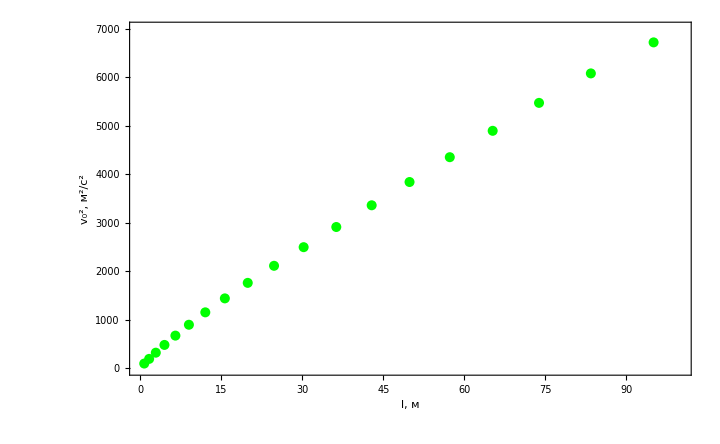

```mathematica
ListPlot[Table[{l[[i]],v0[[i]]^2},{i,1,19}],Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{{0,100},{0,7000}},ImageSize->{720,480},PlotStyle->{Green,PointSize[0.01]},FrameLabel->{Style["l, м", 24],Style["v_0^2, (:043c)^2/(:0441)^2",24]},FrameTicksStyle->18]
```

Строим на графике:

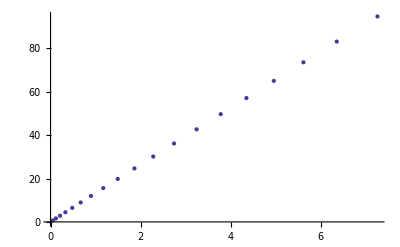

```mathematica
ListPlot[Table[{x[[i]],h[[i]]},{i,1,19}]]
```

Весьма линейная зависимость. Тангенс угла наклона

```mathematica
k=(h.x)/(x.x)
```

13.1026

```mathematica
α=ArcTan[k]/Degree
```

85.6356

Для сравнения:

```mathematica
1.5/Degree//N
```

85.9437

```mathematica
ϕ=Table[z/Degree/.Solve[α-z==(g l[[i]])/(2 v0[[i]]^2 Cos[α])(π/2-z)^2/.α->1.5/.g->9.8,z],{i,1,19}]
```

{{-22.1944,85.7915},{-5.87298,85.7645},{0.235345,85.7517},{4.39167,85.7419},{7.99371,85.7326},{11.4148,85.7229},{14.7364,85.7126},{17.928,85.7018},{20.9123,85.6907},{23.6027,85.6797},{25.9284,85.6695},{27.8526,85.6604},{29.3809,85.6528},{30.5601,85.6466},{31.4726,85.6416},{32.2356,85.6373},{33.0103,85.6328},{34.0474,85.6266},{35.8649,85.6151}}

```mathematica
N[{l[[19]]Sin[ψ[[19,4]]Degree],l[[19]]Sin[ϕ[[19,2]]Degree]},10]
```

{94.7601,94.76}

```mathematica
ψ=Table[z/Degree/.NSolve[Sin[α-z]==(g l[[i]])/(2 v0[[i]]^2 Cos[α])Cos[z]^2/.α->1.5/.g->9.8,z],{i,1,19}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

{{-93.9242,4.06622-76.4115 ⅈ,4.06622+76.4115 ⅈ,85.7918},{-93.9043,4.06974-66.1696 ⅈ,4.06974+66.1696 ⅈ,85.7648},{-93.8952,4.07156-61.6877 ⅈ,4.07156+61.6877 ⅈ,85.7521},{-93.8883,4.07301-58.3647 ⅈ,4.07301+58.3647 ⅈ,85.7423},{-93.8819,4.07445-55.2674 ⅈ,4.07445+55.2674 ⅈ,85.733},{-93.8754,4.076-52.1022 ⅈ,4.076+52.1022 ⅈ,85.7234},{-93.8685,4.07771-48.7782 ⅈ,4.07771+48.7782 ⅈ,85.7131},{-93.8614,4.07956-45.2979 ⅈ,4.07956+45.2979 ⅈ,85.7023},{-93.8542,4.08152-41.725 ⅈ,4.08152+41.725 ⅈ,85.6912},{-93.8473,4.08351-38.165 ⅈ,4.08351+38.165 ⅈ,85.6803},{-93.841,4.08543-34.7489 ⅈ,4.08543+34.7489 ⅈ,85.6701},{-93.8354,4.08718-31.6082 ⅈ,4.08718+31.6082 ⅈ,85.661},{-93.8308,4.08868-28.8445 ⅈ,4.08868+28.8445 ⅈ,85.6534},{-93.8271,4.08992-26.4981 ⅈ,4.08992+26.4981 ⅈ,85.6472},{-93.8241,4.09092-24.5168 ⅈ,4.09092+24.5168 ⅈ,85.6423},{-93.8216,4.0918-22.7197 ⅈ,4.0918+22.7197 ⅈ,85.638},{-93.819,4.09273-20.7271 ⅈ,4.09273+20.7271 ⅈ,85.6335},{-93.8154,4.09402-17.6955 ⅈ,4.09402+17.6955 ⅈ,85.6273},{-93.8088,4.09647-10.3613 ⅈ,4.09647+10.3613 ⅈ,85.6159}}

```mathematica
ϵ=Table[ϕ[[i,2]]-ψ[[i,4]],{i,1,19}]
```

{-0.000294478,-0.000355912,-0.000385947,-0.000409411,-0.000432141,-0.000456152,-0.00048211,-0.000509936,-0.000538958,-0.000568035,-0.000595756,-0.000620766,-0.000642137,-0.00065963,-0.000673817,-0.000686141,-0.000699112,-0.000717239,-0.000751305}

```mathematica
Table[ϕ/Degree/.Solve[ϕ^2(g l[[i]])/(2 v0[[i]]^2 Cos[α])+ϕ(1-π(g l[[i]])/(2 v0[[i]]^2 Cos[α]))+((π^2 g l[[i]])/(8 v0[[i]]^2 Cos[α])-α)==0/.α->1.5/.g->9.8,ϕ],{i,1,19}]
```

{{-22.1944,85.7915},{-5.87298,85.7645},{0.235345,85.7517},{4.39167,85.7419},{7.99371,85.7326},{11.4148,85.7229},{14.7364,85.7126},{17.928,85.7018},{20.9123,85.6907},{23.6027,85.6797},{25.9284,85.6695},{27.8526,85.6604},{29.3809,85.6528},{30.5601,85.6466},{31.4726,85.6416},{32.2356,85.6373},{33.0103,85.6328},{34.0474,85.6266},{35.8649,85.6151}}

```mathematica
Table[%10[[i,2]],{i,1,19}]
```

{85.7915,85.7645,85.7517,85.7419,85.7326,85.7229,85.7126,85.7018,85.6907,85.6797,85.6695,85.6604,85.6528,85.6466,85.6416,85.6373,85.6328,85.6266,85.6151}

```mathematica
Mean[%]
```

85.688

```mathematica
δk=√(((h-k x).(h-k x))/(17Sum[(x[[i]]-Mean[x])^2,{i,1,19}]))
```

0.0205849

```mathematica
Show[ListPlot[Table[{x[[i]],h[[i]]},{i,1,19}]],Plot[k z,{z,0,7.5}]]
```

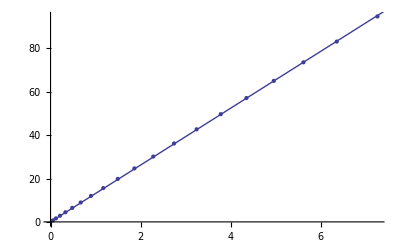

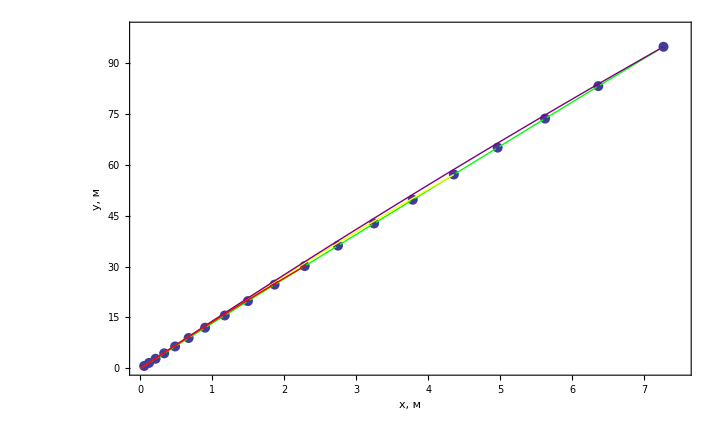

```mathematica
Show[ListPlot[Table[{x[[i]],h[[i]]},{i,1,19}],Axes->False,Frame->True,FrameTicksStyle->20,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{{0,7.5},{0,100}},FrameLabel->{Style["x, м",24],Style["y, м",24]},ImageSize->{720,480},PlotStyle->PointSize[0.01]],Graphics[{Green,BezierCurve[Table[{x[[i]],h[[i]]},{i,1,19}],SplineDegree->10]}],ListPlot[Table[{x[[i]],h[[i]]},{i,1,19}],Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{{0,7.5},{0,100}},FrameLabel->{Style["x, м",24],Style["y, м",24]},ImageSize->{720,480},PlotStyle->PointSize[Medium]],Plot[z Tan[ϕ]-(g z^2)/(2 v0[[15]]^2 Cos[ϕ]^2)/.ϕ->1.5/.g->9.8,{z,0,x[[15]]},PlotStyle->Yellow],Plot[z Tan[ϕ]-(g z^2)/(2 v0[[19]]^2 Cos[ϕ]^2)/.ϕ->1.5/.g->9.8/.i->8,{z,0,x[[19]]},PlotStyle->Purple],Plot[z Tan[ϕ]-(g z^2)/(2 v0[[11]]^2 Cos[ϕ]^2)/.ϕ->1.5/.g->9.8/.i->8,{z,0,x[[11]]},PlotStyle->Red]]
```

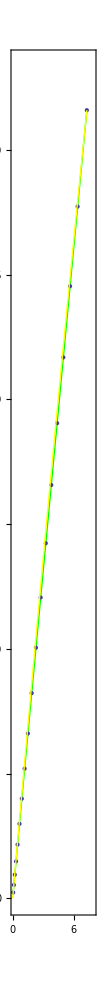

```mathematica
Show[ListPlot[Table[{x[[i]],h[[i]]},{i,1,19}],Axes->False,Frame->True,FrameTicksStyle->20,FrameTicks->{{Automatic,None},{{0,2,4,6,8},None}},PlotRange->{{0,8},{0,100}},ImageSize->{100,600},PlotStyle->PointSize[0.01],AspectRatio->10],Graphics[{Green,BezierCurve[Table[{x[[i]],h[[i]]},{i,1,19}],SplineDegree->10]}],ListPlot[Table[{x[[i]],h[[i]]},{i,1,19}],Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRange->{{0,7.5},{0,100}},ImageSize->{50,200},PlotStyle->PointSize[Medium]],Plot[z Tan[ϕ]-(g z^2)/(2 v0[[19]]^2 Cos[ϕ]^2)/.ϕ->1.5/.g->9.8,{z,0,x[[19]]},PlotStyle->Yellow]]
```

```mathematica
k=ArcTan[Table[h[[i]]/x[[i]],{i,1,19}]]
```

{1.49735,1.49688,1.49666,1.49649,1.49632,1.49615,1.49598,1.49579,1.49559,1.4954,1.49523,1.49507,1.49493,1.49483,1.49474,1.49467,1.49459,1.49448,1.49428}

```mathematica
Rasterize[%,ImageResolution->300]
```

-Graphics-

```mathematica
Clear[x,h]
```

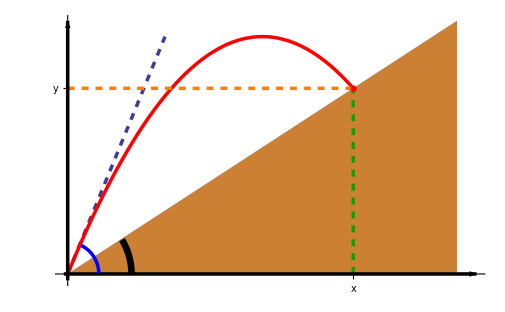

```mathematica
Show[Plot[3x,{x,0,2.5},PlotStyle->{Dashed,Thickness[0.005]},PlotRange->{{-0.1,10.5},{-0.2,8}},ImageSize->{505,410},Ticks->{{{22/3,Style[x,28]}},{{0.8 22/3,Style["y ",28]}}}],Plot[0.8x,{x,0,10},PlotStyle->Thickness[0],Ticks->False,Filling->Axis,FillingStyle->RGBColor[0.8,0.5,0.2]],Plot[0.3x(10-x),{x,0,22/3},PlotStyle->{Red,Thickness[0.005]}],Graphics[{Thickness[0.005],Dashed,Darker[Green],Line[{{22/3,0},{22/3,0.8 22/3}}],Orange,Line[{{0,0.8 22/3},{22/3,0.8 22/3}}]}],Graphics[{Thickness[0.005],Arrow[{{0,-0.2},{0,8}}],Arrow[{{-0.1,0},{10.5,0}}]}],Graphics[{Red,Disk[{22/3,0.8 22/3},{0.08,0.1}]}],Graphics[{Thickness[0.005],Blue,Circle[{0,0},{0.8,1},{0,1.12}]}],Graphics[{Thickness[0.005],Circle[{0,0},{2 0.8,2 1},{0,0.555}],Circle[{0,0},{2.1 0.8,2.1 1},{0,0.555}]}]]
```

```mathematica
Rasterize[%13,ImageResolution->300]
```

-Graphics-

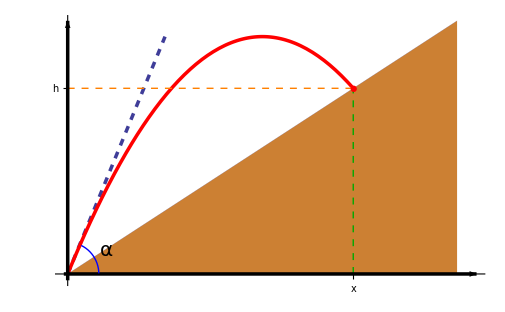

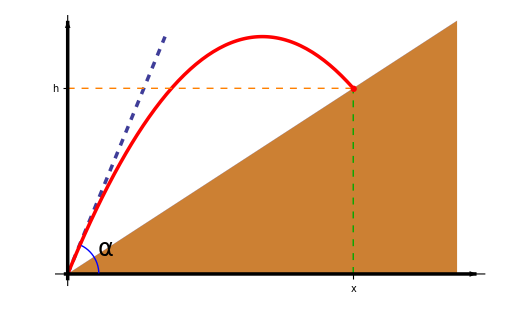

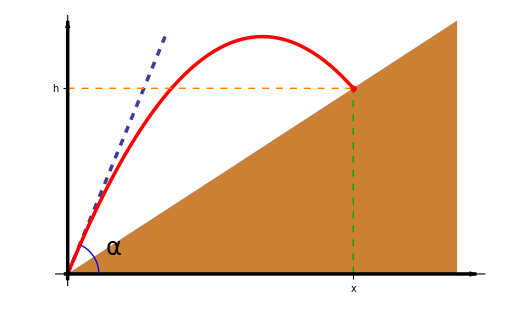
```mathematica
Rasterize[-Graphics-,ImageResolution->300]
```

-Graphics-

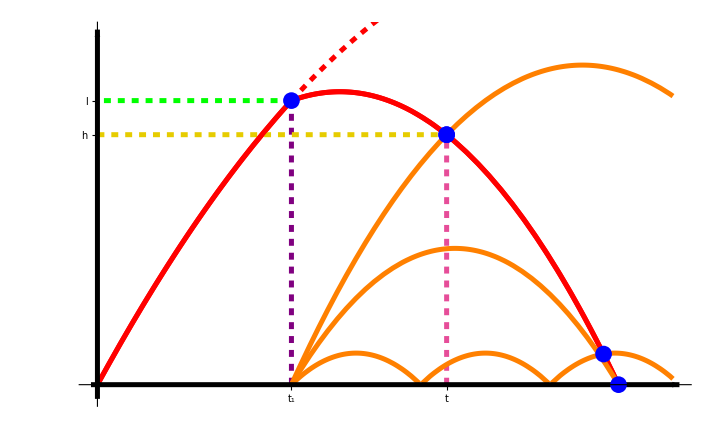

```mathematica
Show[Plot[Piecewise[{{v t-(g t^2)/2/.v->1/3(3^2 g/2+2)/.g->1/9,0<t<3},{2+u(t-3)-(g(t-3)^2)/2/.g->2/9/.u->1/6,3<t<9}}],{t,0,9},Ticks->{{{3,Style[Subscript[t, 1],28]},{27/5,Style[t,28]}},{{2,Style["l ",28]},{44/25,Style["h ",28]}}},PlotRange->{{-0.1,9},{-0.1,2.5}},ImageSize->{720,480},PlotStyle->{Thickness[0.005],Red},TicksStyle->20,RegionFunction->Function[{x,y},y>0.01],AxesStyle->Thickness[0]],Graphics[{Dashed,Thickness[0.005],Purple,Line[{{3,0},{3,2}}],Green,Line[{{3,2},{0,2}}]}],Graphics[{Thickness[0.005],Dashed,RGBColor[0.9,0.8,0],Line[{{0,44/25},{27/5,44/25}}],RGBColor[0.9,0.3,0.6],Line[{{27/5,0},{27/5,44/25}}]}],Plot[Piecewise[{{v t-(g t^2)/2/.v->1/3(3^2 g/2+2)/.g->1/9,0<t<3},{2+u(t-3)-(g(t-3)^2)/2/.g->2/9/.u->1/6,3<t<8.5}}],{t,0,8.5},Ticks->{{{3,Style[Subscript[t, 1],28]}},{{2,Style["l ",28]}}},PlotRange->{{-0.1,8.5},{-0.1,2.5}},ImageSize->{720,480},PlotStyle->{Thickness[0.005],Red},TicksStyle->20,RegionFunction->Function[{x,y},y>0.01],AxesStyle->Thickness[0]],Plot[v t-(g t^2)/2/.v->1/3(3^2 g/2+2)/.g->1/9,{t,3,8.5},PlotStyle->{Red,Thickness[0.005],Dashed},RegionFunction->Function[{x,y},x<8.9]],Plot[v(x-3)-(g (x-3)^2)/2/.g->2/9/.v->1,{x,3,10},PlotStyle->{Thickness[0.005],Orange},RegionFunction->Function[{x,y},y>0.01&&x<8.9]],Plot[g(t-3)(t-3/4 (5+√33))/.g->-0.15,{t,3,10},PlotStyle->{Thickness[0.005],Orange},RegionFunction->Function[{x,y},y>0.01]],Plot[g(t-3-2n)(t-5-2n)/.g->-2/9/.n->{0,1,2,3},{t,3,10},PlotStyle->{Thickness[0.005],Orange},RegionFunction->Function[{x,y},y>0.01&&x<8.9]],Graphics[{Thickness[0.005],Arrow[{{-0.1,0},{9,0}}],Arrow[{{0,-0.1},{0,2.5}}]}],Graphics[{Blue,AbsolutePointSize[12],Point[{27/5,44/25}],Point[{3/4 (5+√33),0}],Point[{27/5,44/25}],Point[{1/4 (49-√313),1/36 (-293+17 √313)}]}],Graphics[{Blue,AbsolutePointSize[12],Point[{3,2}]}]]
```

```mathematica
pwf[t_,t0_,y0_,g_]:=Piecewise[{{((g t0)/2+y0/t0)t-(g t^2)/2,0<t<t0},{y0-8/(9g)(y0/t0-(g t0)/2)^2(4 n^2-n)-((8n)/3+1)(y0/t0-(g t0)/2)*8/(3g)(y0/t0-(g t0)/2)FractionalPart[((t-t0)g)/(8(y0/t0-(g t0)/2)/3)]/.n->IntegerPart[((t-t0)g)/(8(y0/t0-(g t0)/2)/3)],t0≤t}}]
```

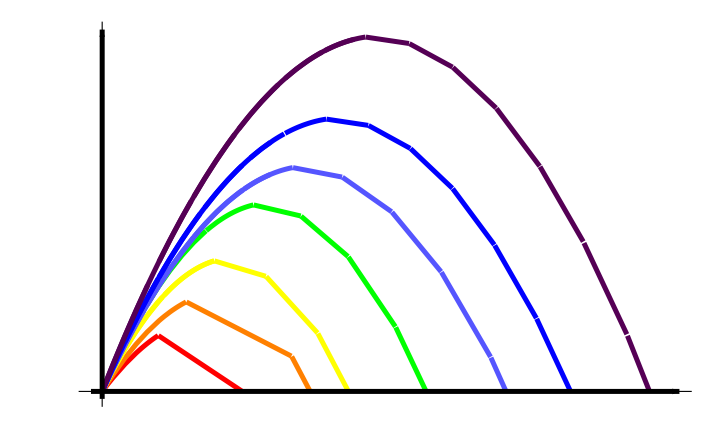

```mathematica
Show[Plot[pwf[t,1,1.5,1],{t,0,10},PlotRange->{{-0.2,10.3},{-0.2,9.7}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Red},ImageSize->{720,480},RegionFunction->Function[{x,y},y>0.01]],Plot[pwf[t,1.5,2.4,1.1],{t,0,10},PlotRange->{{0,10},{0,15}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Orange},ImageSize->{720,480},RegionFunction->Function[{x,y},y>0.01]],Plot[pwf[t,2,3.5,1.3],{t,0,10},PlotRange->{{0,10},{0,15}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Yellow},ImageSize->{720,480},RegionFunction->Function[{x,y},y>0.01]],Plot[((g t0)/2+y0/t0)t-(g t^2)/2/.t0->2/.y0->3.5/.g->1.3,{t,0,2},PlotRange->{{0,10},{0,15}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Yellow},ImageSize->{720,480}],Plot[pwf[t,2.7,5,1.111],{t,0,10},PlotRange->{{0,10},{0,15}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Green},ImageSize->{720,480},RegionFunction->Function[{x,y},y>0.01]],Plot[pwf[t,3.4,6,0.8688],{t,0,10},PlotRange->{{0,10},{0,15}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Lighter[Blue]},ImageSize->{720,480},RegionFunction->Function[{x,y},y>0.01]],Plot[((g t0)/2+y0/t0)t-(g t^2)/2/.t0->3.4/.y0->6/.g->0.8688,{t,0,3},PlotRange->{{0,10},{0,15}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Lighter[Blue]},ImageSize->{720,480}],Plot[pwf[t,4,7.3,0.8],{t,0,10},PlotRange->{{0,10},{0,15}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Blue},ImageSize->{720,480},RegionFunction->Function[{x,y},y>0.01]],Plot[((g t0)/2+y0/t0)t-(g t^2)/2/.t0->4/.y0->7.3/.g->0.8,{t,0,3},PlotRange->{{0,10},{0,15}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Blue},ImageSize->{720,480}],Plot[pwf[t,4.7,9.5,0.7652],{t,0,10},PlotRange->{{0,10},{0,15}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Darker[Purple]},ImageSize->{720,480},RegionFunction->Function[{x,y},y>0.01]],Plot[((g t0)/2+y0/t0)t-(g t^2)/2/.t0->4.7/.y0->9.5/.g->0.7652,{t,0,4.5},PlotRange->{{0,10},{0,15}},Ticks->{None,None},PlotStyle->{Thickness[0.005],Darker[Purple]},ImageSize->{720,480},RegionFunction->Function[{x,y},y>0.01]],Graphics[{Thickness[0.005],Arrow[{{-0.2,0},{10.3,0}}],Arrow[{{0,-0.2},{0,9.7}}]}]]
```

```mathematica
Solve[g(t-3-2n)(t-5-2n)==2+u(t-3)+(g(t-3)^2)/2/.g->-2/9/.n->2/.u->1/6,t]
```

{{t→1/4 (49-√313)},{t→1/4 (49+√313)}}

```mathematica
2+u(t-3)+(g(t-3)^2)/2/.g->-2/9/.n->2/.u->1/6/.t->1/4 (49-√313)//FullSimplify
```

1/36 (-293+17 √313)

```mathematica
Solve[2+u(t-3)-(g(t-3)^2)/2==v(t-3)-(g (t-3)^2)/2/.g->2/9/.u->1/6/.v->1,t]
```

{{t→27/5}}

```mathematica
(t-3)-(g (t-3)^2)/2/.g->2/9/.u->1/6/.v->1/.t->27/5
```

44/25

```mathematica
Manipulate[Graphics[{RGBColor[r,g,b],Disk[]}],{r,0,1},{g,0,1},{b,0,1}]
```

```mathematica
T(1-1/2(√(1+(16l)/(g t^2))+√(1-(16l)/(g t^2))))/.T->5 3600/.l->400/.g->9.8/.t->40
```

396.272

```mathematica
Clear[l]
```

```mathematica
str=OpenRead["D:\\Downloads\\Физика-матем\\Интернетка\\2014-15\\test.dat"]
```

InputStream[D:\Downloads\Физика-матем\Интернетка\2014-15\test.dat,183]

```mathematica
data=Table[{Read[str,String]},{i,1,3}]
```

{{1.2 2},{3 4},{5 6}}

```mathematica
α-ϕ==(g l)/(2 v0^2 Cos[α])(π/2-ϕ)^2/.α->π/2-A/.ϕ->π/2-F
```

-A+F==(F^2 g l Csc[A])/(2 v0^2)

```mathematica
*
```

```mathematica
Clear[ϕ]-Clear[a]^(a:=b)//FullSimplify
```

Null-Null^Null

```mathematica
{Null:=π^4/15-30(ⅇ^(ⅈ Log[-5])+ⅇ^(-ⅈ Log[-5]))+1/4(Tan[Log[Root[#^3-#^2+ⅇ#&]]]),7}
```

SetDelayed::wrsym: Symbol Null is Protected.

{$Failed,7}

```mathematica
%:=2
```

SetDelayed::write: Tag Out in % is Protected.

$Failed

```mathematica
$:=Interpolation[{{0,0},{5,9},{10,7},{-5,3},{-10,1}}]
```

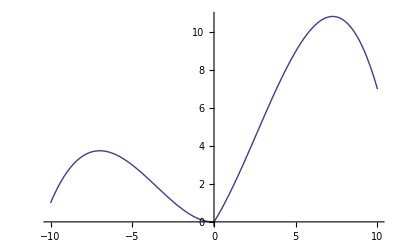

```mathematica
Plot[$[x],{x,-10,10}]
```

```mathematica
$[π]//FullSimplify
```

1/750 π (1025+(180-23 π) π)

```mathematica
Integrate[x^5/(x+1),x]
```

137/60+x-x^2/2+x^3/3-x^4/4+x^5/5-Log[1+x]